```mathematica
f[t_]:=(Cos[t+π/4])^6+(Sin[3t+π/2])^6
```

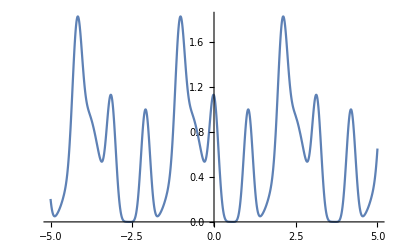

```mathematica
Plot[{f[x]},{x,-5,5}]
```

```mathematica
FunctionPeriod[f[x],x]
```

π

```mathematica
L=2
```

2

```mathematica
a0= 1/(2*L)∫_-L^L (f[x])ⅆx
```

5/8

```mathematica
a[n_]:=1/L∫_-L^L (f[x]*Cos[(n*x*π)/L])ⅆx
```

```mathematica
a[2]
```

-3/16

```mathematica
b[n_]:=1/L*∫_-L^L f[x]*Sin[(n*x*π)/L]ⅆx
```

```mathematica
d3=a0+∑_(n=1)^20 (a[n]*Cos[(n*x*π)/L]+b[n]*Sin[(n*x*π)/L])
```

5/8-3/16 Cos[4 x]+15/32 Cos[6 x]+3/16 Cos[12 x]+1/32 Cos[18 x]-15/32 Sin[2 x]+1/32 Sin[6 x]

```mathematica
cn[n_]:=  1/(2*L)∫_-L^L f[x]*ⅇ^(-ⅈ*(n*π*x)/L)ⅆx
```

```mathematica
sum=∑_(n=-20)^20 cn[n]*ⅇ^(ⅈ*(n*π*x)/L)
```

5/8-15/64 ⅈ ⅇ^(-2 ⅈ x)+15/64 ⅈ ⅇ^(2 ⅈ x)-3/32 ⅇ^(-4 ⅈ x)-3/32 ⅇ^(4 ⅈ x)+(15/64+ⅈ/64) ⅇ^(-6 ⅈ x)+(15/64-ⅈ/64) ⅇ^(6 ⅈ x)+3/32 ⅇ^(-12 ⅈ x)+3/32 ⅇ^(12 ⅈ x)+1/64 ⅇ^(-18 ⅈ x)+1/64 ⅇ^(18 ⅈ x)

```mathematica
g[t_]:=(Cos[t])^6+(Sin[t])^4
```

```mathematica
FunctionPeriod[g[x],x]
```

π

```mathematica
cn2[n_]:=  1/(2*L)∫_-L^L g[x]*ⅇ^(-ⅈ*(n*π*x)/L)ⅆx
```

```mathematica
sum=∑_(n=-20)^20 cn2[n]*ⅇ^(ⅈ*(n*π*x)/L)
```

11/16-1/64 ⅇ^(-2 ⅈ x)-1/64 ⅇ^(2 ⅈ x)+5/32 ⅇ^(-4 ⅈ x)+5/32 ⅇ^(4 ⅈ x)+1/64 ⅇ^(-6 ⅈ x)+1/64 ⅇ^(6 ⅈ x)

```mathematica
g''[x]
```

-6 Cos[x]^6+12 Cos[x]^2 Sin[x]^2+30 Cos[x]^4 Sin[x]^2-4 Sin[x]^4

```mathematica
g1[x_]:= (-6Cos[x])^5*Sin[x]+4*Cos[x]*(Sin[x])^3
```

```mathematica
g1[x]
```

-7776 Cos[x]^5 Sin[x]+4 Cos[x] Sin[x]^3

```mathematica
cn21[n_]:=  1/(2*L)∫_-L^L g'[x]*ⅇ^(-ⅈ*(n*π*x)/L)ⅆx
```

```mathematica
sum=∑_(n=-20)^20 cn21[n]*ⅇ^(ⅈ*(n*π*x)/L)
```

1/32 ⅈ ⅇ^(-2 ⅈ x)-1/32 ⅈ ⅇ^(2 ⅈ x)-5/8 ⅈ ⅇ^(-4 ⅈ x)+5/8 ⅈ ⅇ^(4 ⅈ x)-3/32 ⅈ ⅇ^(-6 ⅈ x)+3/32 ⅈ ⅇ^(6 ⅈ x)

```mathematica
cn22[n_]:=  1/(2*L)∫_-L^L g''[x]*ⅇ^(-ⅈ*(n*π*x)/L)ⅆx
```

```mathematica
sum=∑_(n=-20)^20 cn22[n]*ⅇ^(ⅈ*(n*π*x)/L)
```

1/16 ⅇ^(-2 ⅈ x)+1/16 ⅇ^(2 ⅈ x)-5/2 ⅇ^(-4 ⅈ x)-5/2 ⅇ^(4 ⅈ x)-9/16 ⅇ^(-6 ⅈ x)-9/16 ⅇ^(6 ⅈ x)

```mathematica
f[x_]:= Piecewise[{{-x-1, -2<x<-1},{x+1, -1<x<0},{(x-1)^2,0<x<2}}]
```

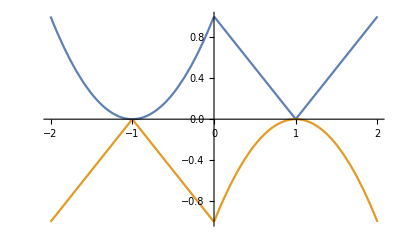

```mathematica
Plot[{ f[-x],-f[x]},{x,-2,2}]
```

```mathematica
a01= 1/(2*L)∫_-L^L (f[x])ⅆx
```

5/12

```mathematica
ab[n_]:=1/L∫_-L^L (f[x]*Cos[(n*x*π)/L])ⅆx
```

```mathematica
bb[n_]:=1/L*∫_-L^L f[x]*Sin[(n*x*π)/L]ⅆx
```

```mathematica
db3=a01+∑_(n=1)^10 (ab[n]*Cos[(n*x*π)/L]+bb[n]*Sin[(n*x*π)/L])
```

5/24-(2 (16-6 π+2 √2 π-π^2) Cos[(π x)/4])/π^3+(2 (16+18 π+6 √2 π-9 π^2) Cos[(3 π x)/4])/(27 π^3)+(2 Cos[π x])/π^2+(2 (-16+30 π+10 √2 π+25 π^2) Cos[(5 π x)/4])/(125 π^3)-(2 (-16-42 π+14 √2 π+49 π^2) Cos[(7 π x)/4])/(343 π^3)+Cos[2 π x]/(4 π^2)-(2 (16-54 π+18 √2 π-81 π^2) Cos[(9 π x)/4])/(729 π^3)+(4 (-8+π+√2 π) Sin[(π x)/4])/π^3+(2 (-4+π) Sin[(π x)/2])/π^3+(4 (-8-3 π+3 √2 π) Sin[(3 π x)/4])/(27 π^3)-(4 (8-5 π+5 √2 π) Sin[(5 π x)/4])/(125 π^3)-(2 (4+3 π) Sin[(3 π x)/2])/(27 π^3)-(4 (8+7 π+7 √2 π) Sin[(7 π x)/4])/(343 π^3)+(4 (-8+9 π+9 √2 π) Sin[(9 π x)/4])/(729 π^3)+(2 (-4+5 π) Sin[(5 π x)/2])/(125 π^3)

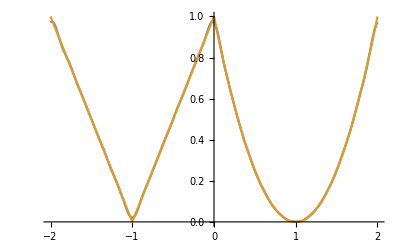

```mathematica
Plot[{db3,f[x]},{x,-2,2}]
```

```mathematica
a[x_]:=11/16-1/64 ⅇ^(-2 ⅈ x)-1/64 ⅇ^(2 ⅈ x)+5/32 ⅇ^(-4 ⅈ x)+5/32 ⅇ^(4 ⅈ x)+1/64 ⅇ^(-6 ⅈ x)+1/64 ⅇ^(6 ⅈ x)
```

```mathematica
a'[x]
```

1/32 ⅈ ⅇ^(-2 ⅈ x)-1/32 ⅈ ⅇ^(2 ⅈ x)-5/8 ⅈ ⅇ^(-4 ⅈ x)+5/8 ⅈ ⅇ^(4 ⅈ x)-3/32 ⅈ ⅇ^(-6 ⅈ x)+3/32 ⅈ ⅇ^(6 ⅈ x)